## Resolución del sistema

```mathematica
Clear[β, Ω, alphaMas, alphaMenos, alphaZ]
```

Valores de los parámetros

```mathematica
β = 0.1; Ω = 0.3;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + I Ω(1 + x[t]^2)== 0 ,y'[t] == I(Ω x[t] - Tanh[(β t)/2]),z'[t]Exp[-2 y[t]]+ I Ω == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Length[(alphaZ)@ValuesOnGrid]
```

14123

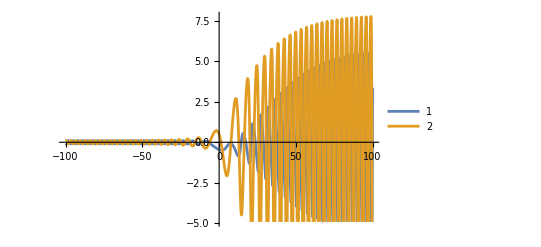

```mathematica
Plot[{Im[alphaMas[t]], -Im[alphaMenos[t]]}, {t,-100,100}, PlotLegends->Automatic]
```

## Probabilidades de Transición

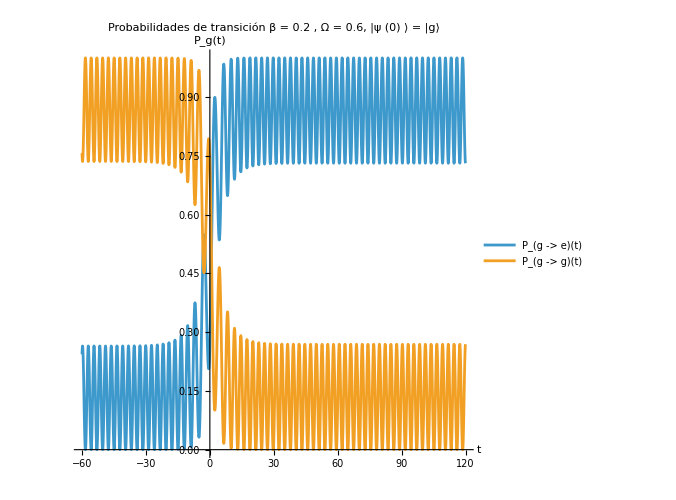

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -60, 120}, PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)"},
PlotLabel->Style["Probabilidades de transición  β = 0.2 , Ω = 0.6, |ψ (0) ⟩ = |g⟩ ", 16, FontFamily->"Times New Roman", Black],
AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta02/omega06/probabilidades1.png",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta02/omega06/probabilidades1.png

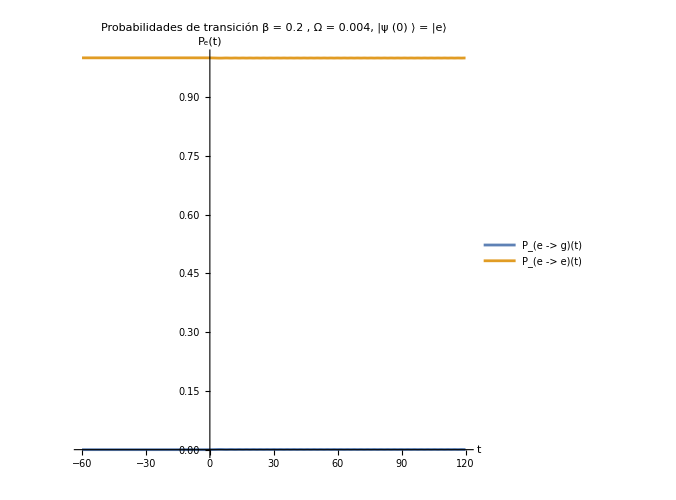

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2}, {t, -60, 120}, 
PlotLabel->Style["Probabilidades de transición  β = 0.2 , Ω = 0.004, |ψ (0) ⟩ = |e⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)"},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

## Espectro EW estado base

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S1[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
G1 = ListLinePlot[ParallelTable[{ω,S1[0.1,ω,220,-240]},{ω,-3.2,3.8,0.025}],PlotRange->{-0.05,20.2},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=120",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]],
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.1, Ω = 0.3, Γ = 0.1,", 14, FontFamily->"Times New Roman", Black]]
```

$Aborted

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta01/omega03/general/t=220",G1,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta01/omega03/general/t=220

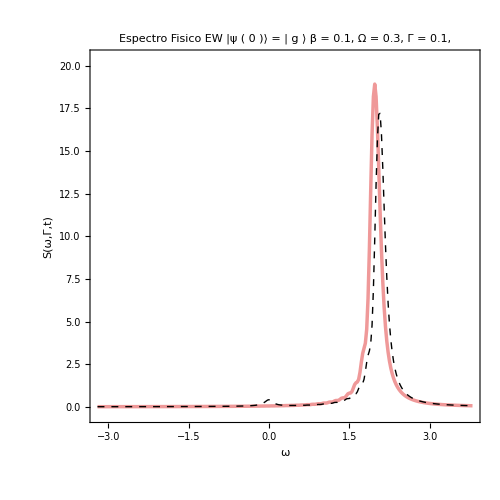

```mathematica
Show[ListLinePlot[ParallelTable[{Δ,NumEW2Tanh[0.1,0.1,Δ,-240,70]},{Δ,-3.2,3.8,0.025}],PlotRange->{-0.5,20.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotLegends->"Analitico (Rojo)", PlotStyle->Directive[Thickness[0.005], RGBColor[0.85,0,0], Opacity[0.4]],
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500],
 ListLinePlot[ParallelTable[{ω,S1[0.1,ω,70,-240]},{ω,-3.2,3.8,0.025}],PlotRange->{-0.05,20.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002], Dashed],PlotLegends->"t=70",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->450],
PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.1, Ω = 0.3, Γ = 0.1,", 14, FontFamily->"Times New Roman", Black]
]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta01/omega03/comparacion/t=70",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/hiperbolico/interaccion_fuerte/beta01/omega03/comparacion/t=70

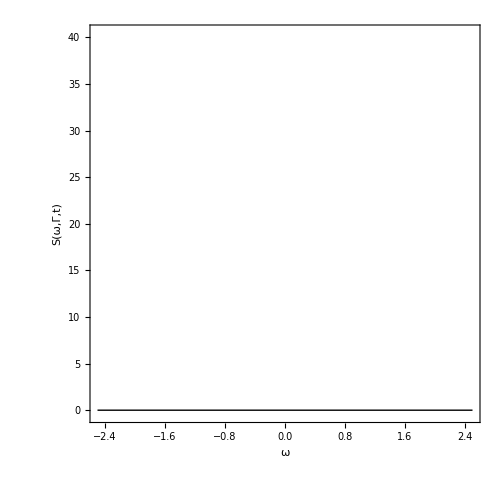

```mathematica
G2 = ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω,-40,-200]},{ω,-2.5,2.5,0.025}],PlotRange->{-0.5,40.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

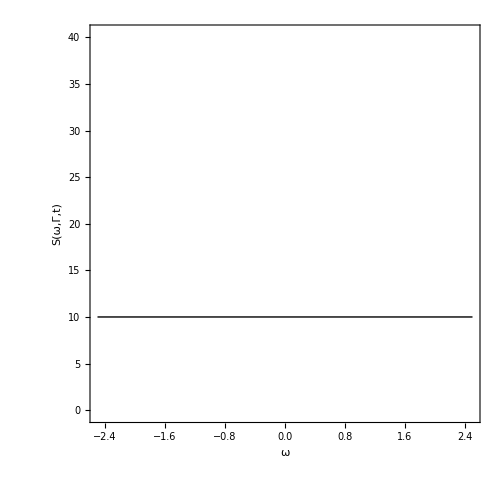

```mathematica
G3 =  ListLinePlot[ParallelTable[{ω,10+S1[0.1,ω,-20,-200]},{ω,-2.5,2.5,0.025}],PlotRange->{-0.5,40.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-20",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

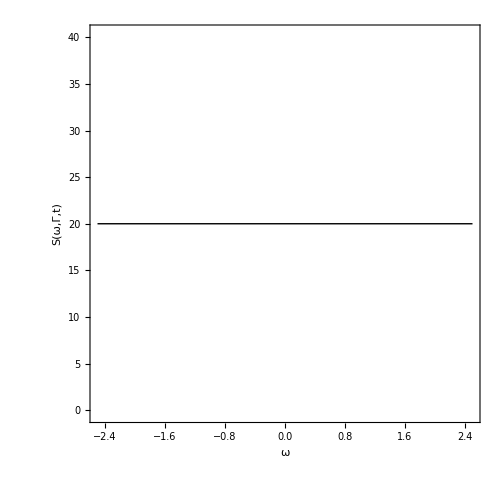

```mathematica
G4 =  ListLinePlot[ParallelTable[{ω,20+S1[0.1,ω,0,-200]},{ω,-2.5,2.5,0.025}],PlotRange->{-0.5,40.5},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=0",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

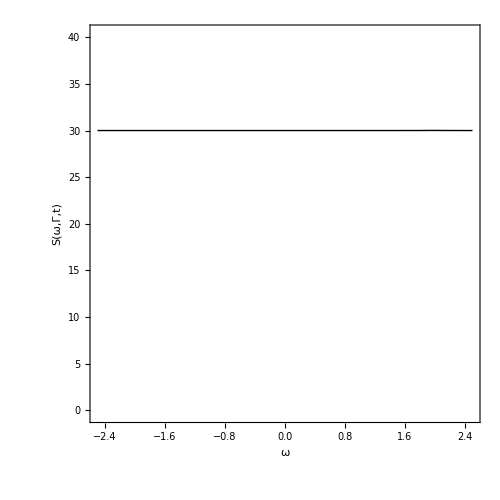

```mathematica
G5 = ListLinePlot[ParallelTable[{ω,30+S1[0.1,ω,40,-200]},{ω,-2.5,2.5,0.025}],PlotRange->{-0.5,40.5},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Black],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Black]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

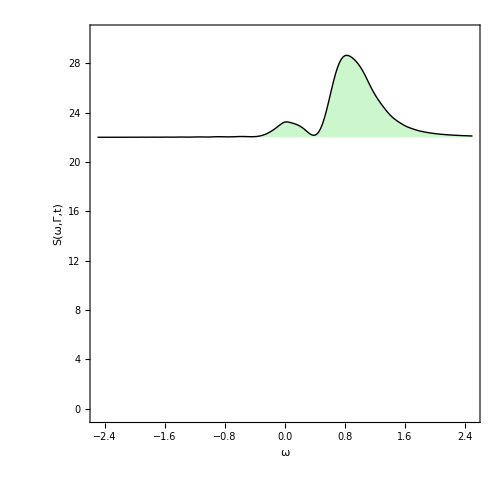

```mathematica
G6 = ListLinePlot[ParallelTable[{ω,22+S1[0.1,ω,14,-200]},{ω,-2.5,2.5,0.025}],PlotRange->{-0.5,30.5},Filling->22,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=14",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

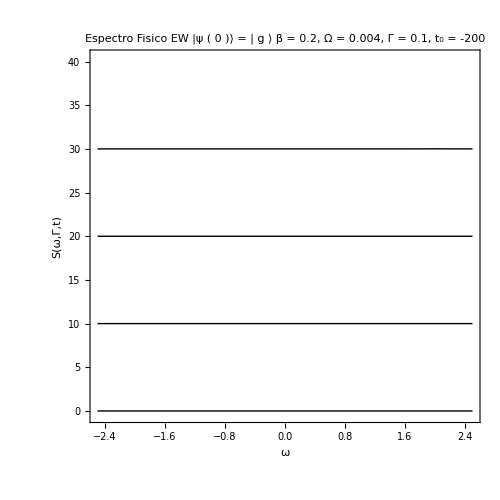

```mathematica
Show[G5,G4,G3,G2, PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.2, Ω = 0.004, Γ = 0.1, t_0 = -200 ", 16, FontFamily->"Times New Roman", Black]]
```

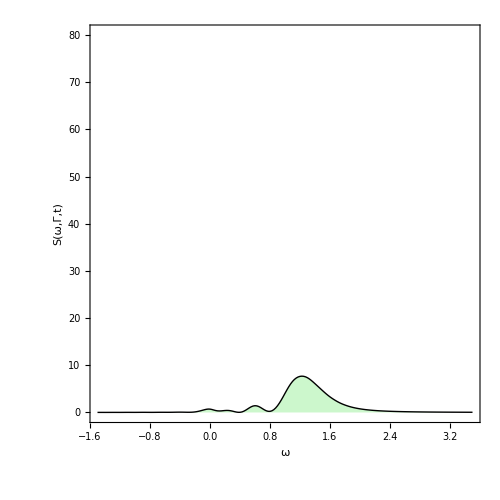

```mathematica
G8 =  ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω,20,-200]},{ω,-1.5,3.5,0.025}],PlotRange->{-0.5,80.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

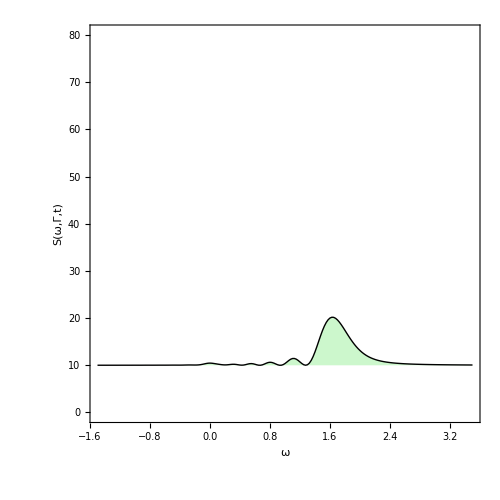

```mathematica
G9 = ListLinePlot[ParallelTable[{ω,10+S1[0.1,ω,30,-200]},{ω,-1.5,3.5,0.025}],PlotRange->{-0.5,80.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

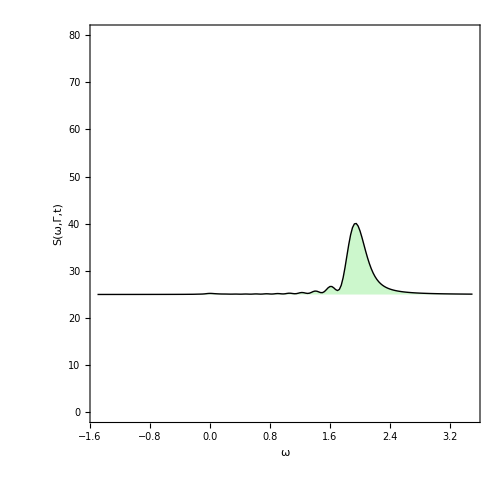

```mathematica
G10 = ListLinePlot[ParallelTable[{ω,25+S1[0.1,ω,50,-200]},{ω,-1.5,3.5,0.025}],PlotRange->{-0.5,80.5},Filling->25,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=50",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

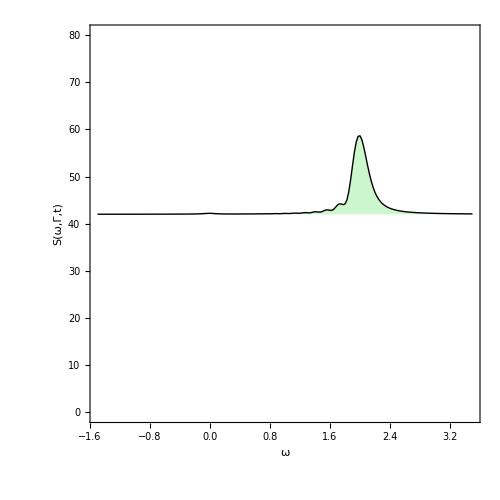

```mathematica
G11 =ListLinePlot[ParallelTable[{ω,42+S1[0.1,ω,60,-200]},{ω,-1.5,3.5,0.025}],PlotRange->{-0.5,80.5},Filling->42,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=60",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

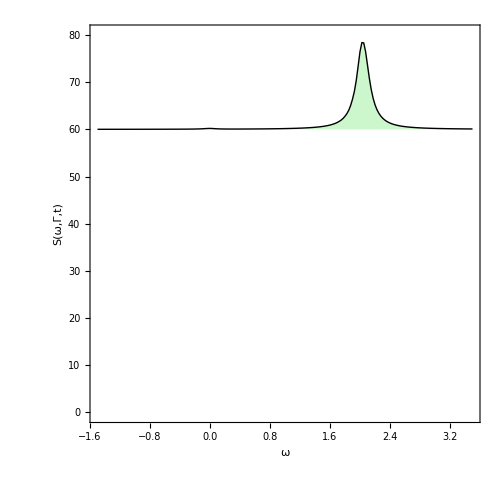

```mathematica
G12 = ListLinePlot[ParallelTable[{ω,60+S1[0.1,ω,100,-200]},{ω,-1.5,3.5,0.025}],PlotRange->{-0.5,80.5},Filling->60,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=100",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

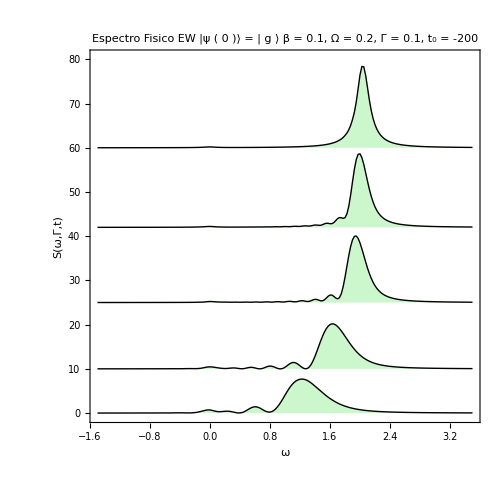

```mathematica
Show[G12,G11,G10,G9,G8, PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```

## Espectro EW estado excitado

```mathematica
Clear[L1,L2]
```

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

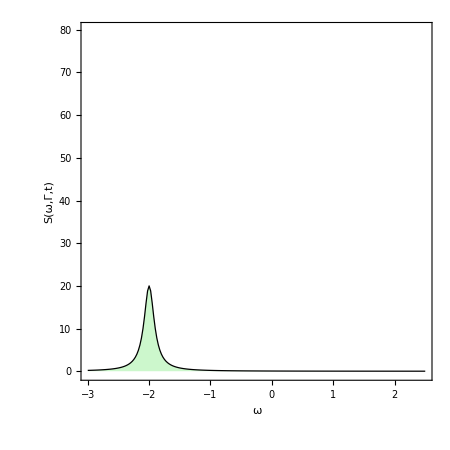

```mathematica
W1 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-40,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-40",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

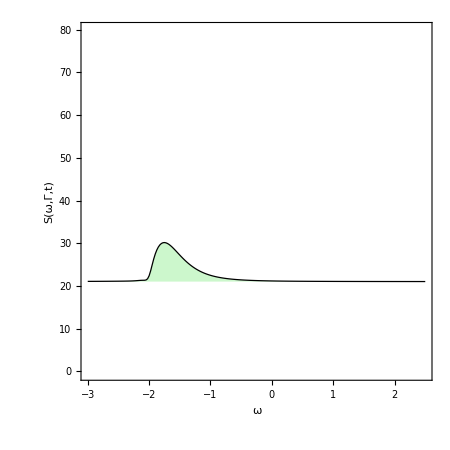

```mathematica
W2 =ListLinePlot[ParallelTable[{ω,21+S2[0.1,ω,-6,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->21,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-6",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

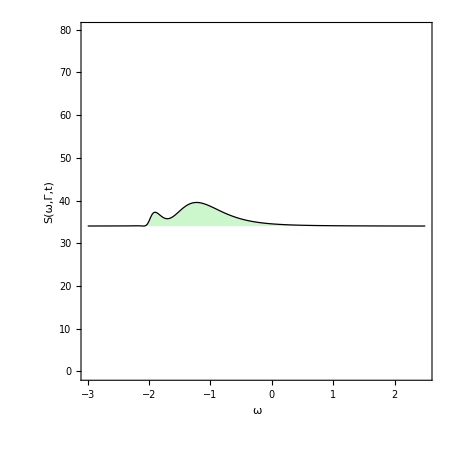

```mathematica
W3 =ListLinePlot[ParallelTable[{ω,34+S2[0.1,ω,-2,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->34,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-2",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

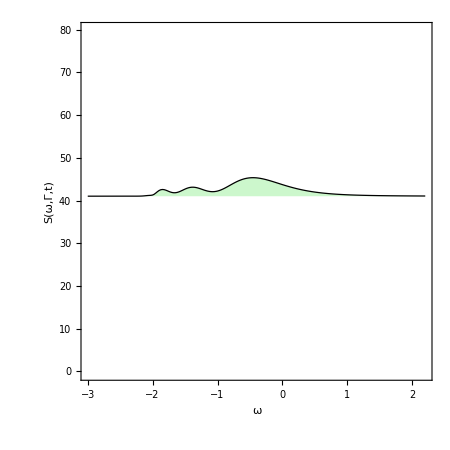

```mathematica
W4 =ListLinePlot[ParallelTable[{ω,41+S2[0.1,ω,2,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->41,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=2",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

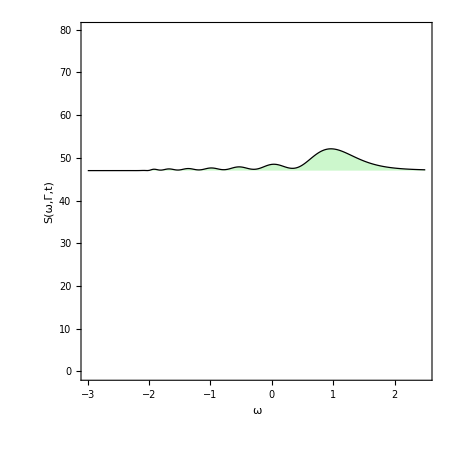

```mathematica
W5 =ListLinePlot[ParallelTable[{ω,47+S2[0.1,ω,10,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->47,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

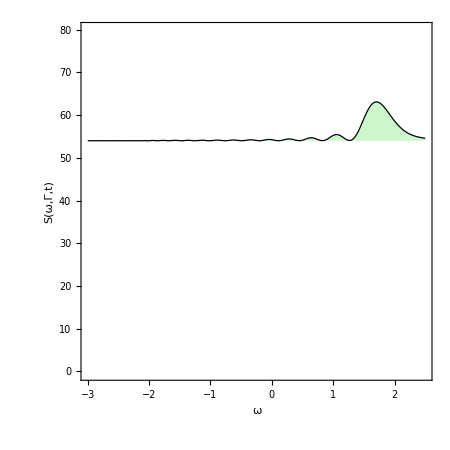

```mathematica
W6 =ListLinePlot[ParallelTable[{ω,54+S2[0.1,ω,20,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,80.1},Filling->54,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

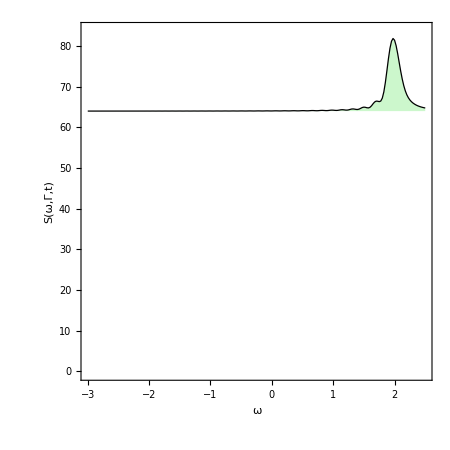

```mathematica
W7 =ListLinePlot[ParallelTable[{ω,64+S2[0.1,ω,44,-200]},{ω,-3.0,2.5,0.025}],PlotRange->{-0.5,84.1},Filling->64,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=44",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

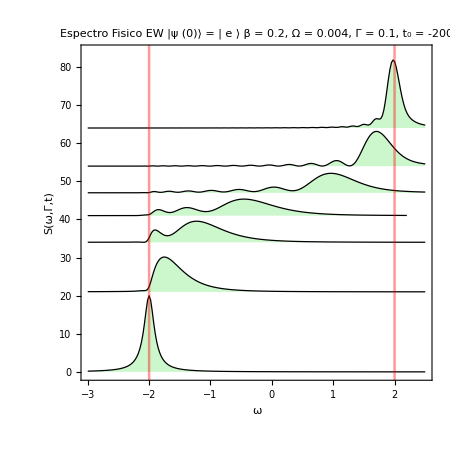

```mathematica
Show[W7,W6,W5,W4,W3,W2,W1,GridLines->{{{-2.0,Directive[Thickness[0.004],Red]},{+2.0,Directive[Thickness[0.004],Red]}},None},
PlotLabel->Style["Espectro Fisico EW   |ψ (0)⟩ = | e ⟩ \n β = 0.2, Ω = 0.004, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```

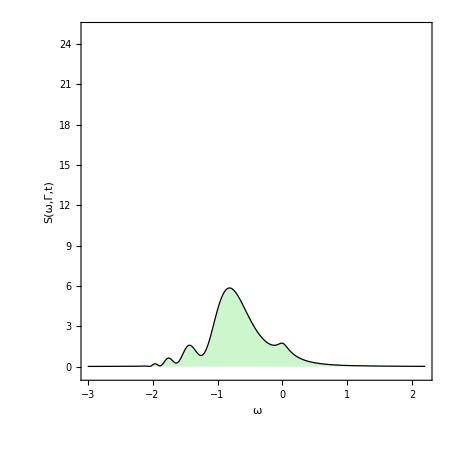

```mathematica
W10 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-1,-200]},{ω,-3.0,2.2,0.025}],PlotRange->{-0.5,25.1},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-1",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

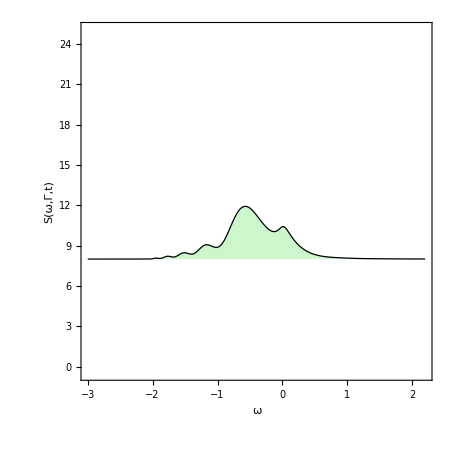

```mathematica
W11 =ListLinePlot[ParallelTable[{ω,8+S2[0.1,ω,3,-200]},{ω,-3.0,2.2,0.025}],PlotRange->{-0.5,25.1},Filling->8,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=3",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

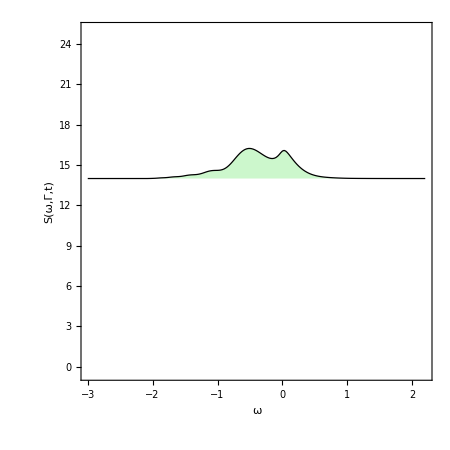

```mathematica
W12 =ListLinePlot[ParallelTable[{ω,14+S2[0.1,ω,6,-200]},{ω,-3.0,2.2,0.025}],PlotRange->{-0.5,25.1},Filling->14,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=6",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

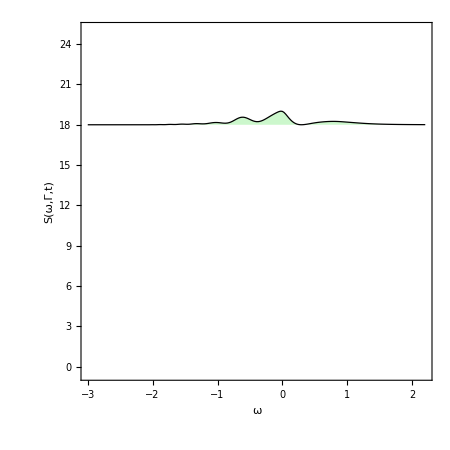

```mathematica
W13 =ListLinePlot[ParallelTable[{ω,18+S2[0.1,ω,14,-200]},{ω,-3.0,2.2,0.025}],PlotRange->{-0.5,25.1},Filling->18,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=14",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

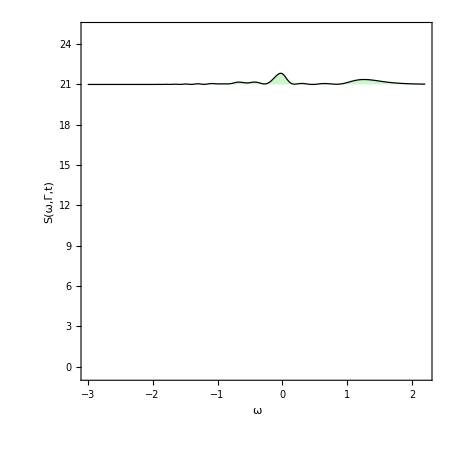

```mathematica
W14 =ListLinePlot[ParallelTable[{ω,21+S2[0.1,ω,20,-200]},{ω,-3.0,2.2,0.025}],PlotRange->{-0.5,25.1},Filling->21,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->450,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

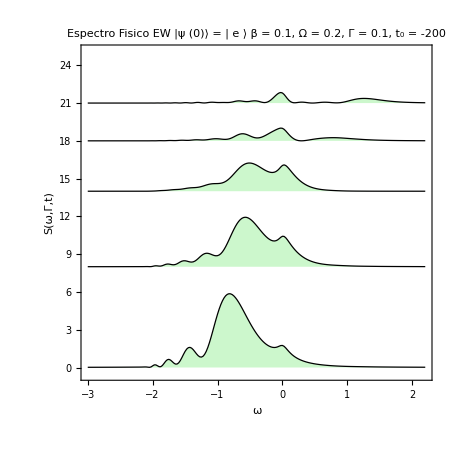

```mathematica
Show[W14,W13,W12,W11,W10,PlotLabel->Style["Espectro Fisico EW   |ψ (0)⟩ = | e ⟩ \n β = 0.1, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```

## Caso desacoplado Comparación

```mathematica
NumEW2Tanh[Γ_,β_,Δ_,to_,T_]:=2Γ Exp[-2 Γ T]*(Abs[NIntegrate[Exp[(Γ -I Δ )t+I (4/β) Log[Cosh[ β t/2]]],{t,to,T}]]^2)
```

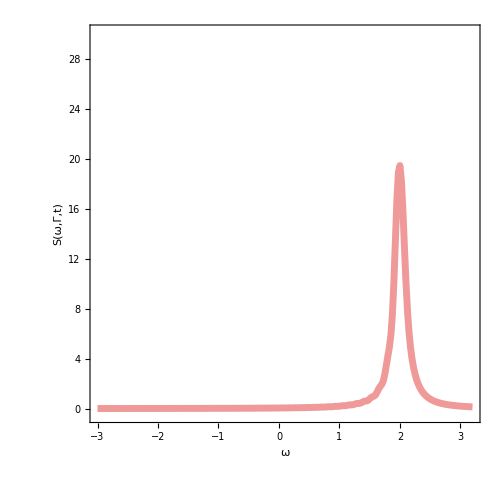

```mathematica
C1 = ListLinePlot[ParallelTable[{Δ,NumEW2Tanh[0.1,0.2,Δ,-200,60]},{Δ,-3.0,3.2,0.025}],PlotRange->{-0.5,30.1},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotLegends->"Analitico (Rojo)", PlotStyle->Directive[Thickness[0.01], RGBColor[0.85,0,0], Opacity[0.4]],
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500]
```

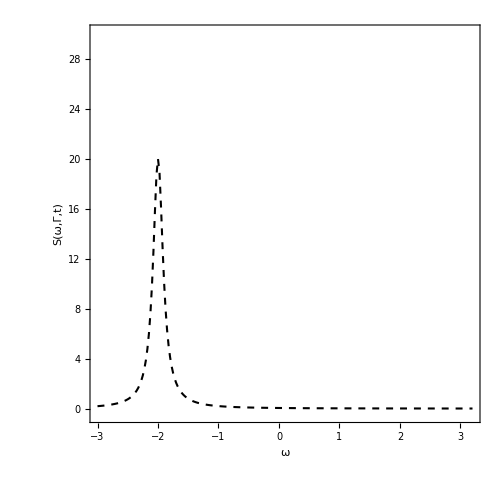

```mathematica
C2 = ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-30,-200]},{ω,-3.0,3.2,0.025}],PlotRange->{-0.5,30.1},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Thickness[0.003],Black, Dashed],PlotLegends->"Numerico (Dashed)",
FrameLabel->{Style["ω",30,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",25,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1, ImageSize->500]
```

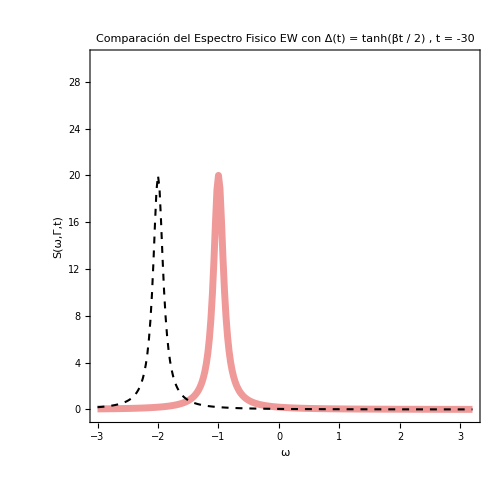

```mathematica
Show[C1,C2, PlotLabel->Style["Comparación del Espectro Fisico EW con \n Δ(t) = tanh(βt / 2) , t = -30", 16, FontFamily->"Times New Roman", Black]]
```

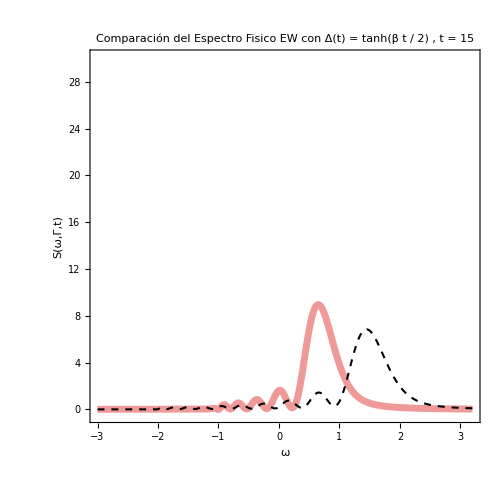

```mathematica
Show[C1,C2, PlotLabel->Style["Comparación del Espectro Fisico EW con \n Δ(t) = tanh(β t / 2) , t = 15", 16, FontFamily->"Times New Roman", Black]]
```